```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/critical_region/LPA/phaseboundary/mub50/buffer

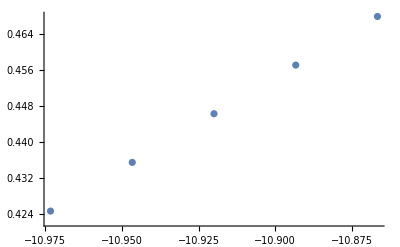

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
T=Flatten[Import["./TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
csdata=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
a1=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[T]-2}];
b1200=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}];
Show[ListPlot[{csdata},PlotRange->All]]
```

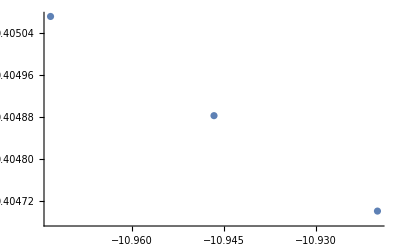

```mathematica
ListPlot[Transpose[{Log[-t[[2;;Length[t]-2]]],b1200}],PlotRange->All]
```